# Test and Filter Runs

n: number of stars
NS: number of simulations
R: virial radius
Isolated System

### Logs

```mathematica
Print[$RunNumber]
```

300

```mathematica
Print[script`path]
```

/home/cesarg/git/workspace/nbody6/isolated/scripts/FilterAndTest

```mathematica
logstream = OpenWrite[
FileNameJoin[{script`path, "nbstatus" <> ToString[$RunNumber] <> ".log"}],
FormatType->OutputForm
]
```

OutputStream[…]

```mathematica
Write[logstream, "Begin log ...."];
```

## Initialization

```mathematica
{$MachineName,$Version}
```

{tars,12.1.0 for Linux x86 (64-bit) (March 18, 2020)}

```mathematica
AppendTo[$Path,Environment["MYGITDIR"]];
```

```mathematica
Get["AstroTools`nbody6`"]
```

```mathematica
Get["AstroTools`Utilities`"]
```

```mathematica
$ConfiguredKernels = 
 List[SubKernels`LocalKernels`LocalMachine[30, 
   Rule[SubKernels`LocalKernels`LowerPriority, True]]]
```

{SubKernels`LocalKernels`LocalMachine[30,SubKernels`LocalKernels`LowerPriority→True]}

```mathematica
resultsPath=FileNameJoin[{Environment["MYGITDIR"],"workspace","nbody6","isolated","n"<>ToString[$RunNumber],"NSX-R1","results"}]
```

/home/cesarg/git/workspace/nbody6/isolated/n300/NSX-R1/results

```mathematica
SetDirectory[resultsPath]
```

/home/cesarg/git/workspace/nbody6/isolated/n300/NSX-R1/results

```mathematica
FileNames[]
```

{goodRuns.log,move.sh,.move.sh.swp,run-10,run-100,run-11,run-12,run-13,run-14,run-15,run-16,run-17,run-20,run-25,run-26,run-28,run-29,run-36,run-37,run-38,run-41,run-42,run-43,run-45,run-47,run-49,run-50,run-51,run-52,run-53,run-55,run-6,run-61,run-62,run-63,run-64,run-68,run-69,run-70,run-71,run-72,run-73,run-76,run-77,run-83,run-87,run-89,run-93,run-97,temp}

### n–body parameters

```mathematica
(*
numberOfStars=380;
nb["S0"]=0.3(numberOfStars/1000)^(1/3)
nb["nMAX"]=2.(numberOfStars)^(1/2)
*)
```

```mathematica
FilePrint["../create-ini.sh"]
```

#!/bin/bash
# first group 1-250

echo "[`date`] Start"

mkdir results

cd results/
for filenumber in {1..500..1}
do
	mkdir "./run-$filenumber/"
  	cat << EOF > ./run-$filenumber/ini.dat
1 20.0
300 1 10 $RANDOM 38 1
0.02 0.01 0.2 2.0 1.0 1201.0 1.0E-03 1 0.5
0 0 1 0 1 0 0 0 2 0
0 0 0 0 0 0 0 0 0 6
0 0 0 0 0 0 0 0 0 0
0 0 0 0 0 0 0 0 0 1
0 0 0 0 0 0 0 0 0 0
4.0E-05 0.001 0.2 1.0 1.0E-06 0.001
2.3 50.0 0.2 0 0 0.002 0 5.0
0.5 0 0 0 0.5
EOF

done

cd ..
echo `pwd`
echo "[`date`] End"
echo "time elapsed: $SECONDS"
echo all done

```mathematica
strCreateFile=Import["../create-ini.sh","Table"]
```

{{#!/bin/bash},{#,first,group,1-250},{},{echo,[`date`] Start},{},{mkdir,results},{},{cd,results/},{for,filenumber,in,{1..500..1}},{do},{mkdir,./run-$filenumber/},{cat,<<,EOF,>,./run-$filenumber/ini.dat},{1,20.},{300,1,10,$RANDOM,38,1},{0.02,0.01,0.2,2.,1.,1201.,0.001,1,0.5},{0,0,1,0,1,0,0,0,2,0},{0,0,0,0,0,0,0,0,0,6},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0},{0.00004,0.001,0.2,1.,1.×10^-6,0.001},{2.3,50.,0.2,0,0,0.002,0,5.},{0.5,0,0,0,0.5},{EOF},{},{done},{},{cd,..},{echo,`pwd`},{echo,[`date`] End},{echo,time elapsed: $SECONDS},{echo,all,done}}

```mathematica
pos=Position[strCreateFile,"$RANDOM"][[1,1]];
numberOfStars=strCreateFile[[pos,1]]
nbodyStep=Floor@(strCreateFile[[pos+1,5]])
maxNbodyTime=Floor@(strCreateFile[[pos+1,6]]-nbodyStep)
```

300

1

1200

### Other global variables

#### Data

```mathematica
goodFiles=FileNameJoin[First[#]]&/@GatherBy[StringSplit[Import["goodRuns.log"][[All,2]],"/"],#[[-2]]&];
```

```mathematica
dirs=DirectoryName/@goodFiles;
```

```mathematica
runmax=Length[dirs]
```

46

```mathematica
If[!FileExistsQ["nbody6-data.mx"]
,
Print["Loading from source ..."];
data=ReadOutput/@goodFiles;
DumpSave["nbody6-data.mx",data];
,
Print["Loading from MX ..."];
Get["nbody6-data.mx"];
]//AbsoluteTiming
```

Loading from source ...

ReadList::readn: Invalid real number found when reading from «1».

General::stop: Further output of «1» will be suppressed during this calculation.

{14.8793,Null}

```mathematica
parameters=data[[All,1]];
```

```mathematica
parameters//Length
```

46

```mathematica
data=data[[All,2]];
```

```mathematica
lengthOfRuns=Tally[Length/@data]
```

{{1201,46}}

#### Parameters

```mathematica
(* NOTE 1: parameters V^*, T^*, M^* are different for each run *)
(* NOTE 2: $MeanMass numberOfStats ≈ $MassScale *)
parameters[[All,4]]
```

{0.955,0.845,1.003,0.922,0.842,0.92,0.896,1.009,0.946,0.986,0.907,0.84,0.937,0.909,1.071,0.922,0.839,0.967,0.883,0.976,0.916,0.94,0.982,0.902,0.845,1.008,0.933,0.957,0.911,0.856,0.928,1.032,0.904,0.942,1.023,1.013,0.827,0.995,0.91,0.851,0.933,0.988,0.941,0.928,0.928,0.998}

```mathematica
{$LengthScale,$MassScale,$SpeedScale,$TimeScale,$MeanMass,$SU}=Mean[parameters]
```

{1.,257.754,1.05083,0.934043,0.859565,4.4×10^7}

```mathematica
$EnergyScale=$MassScale ($SpeedScale)^2
```

284.621

```mathematica
$DensityScale=$MassScale/($LengthScale)^3
```

257.754

```mathematica
(* in units of Msun/pc^3*)
ρSunNeighborPhysical=0.09;
ρForClusterDisruptionPhysical=0.08;
```

```mathematica
(* in units of n-body units *)
ρSunNeighbor=ρSunNeighborPhysical/$DensityScale;
ρForClusterDisruption=ρForClusterDisruptionPhysical/$DensityScale;
```

```mathematica
(* checking units *)
ρSunNeighbor
```

0.00034917

```mathematica
(* mean density in nbody units *)
$MeanDensity=1./(4/3Pi(1)^3)
```

0.238732

```mathematica
(* mean density physical Msun/pc^3 *)
$MeanDensity $DensityScale
```

61.5343

```mathematica
(* Max elpased time for evolution in MY*)
maxNbodyTime*$TimeScale
```

1120.85

```mathematica
(* INITIAL TIME = 0 -> following nbody6 *)
timeArray=Range[0,maxNbodyTime,nbodyStep];
(* log step array: 0 time at -1 *)
log10TimeArray1=N@Prepend[Log10[Rest[timeArray]],0];
log10TimeArrayScaled1=N@Prepend[Log10[Rest[$TimeScale timeArray]],0];
```

```mathematica
Length/@{timeArray,log10TimeArray1,log10TimeArrayScaled1}
```

{1201,1201,1201}

## Delete invalid runs

```mathematica
dirsToDelete=Complement[Select[FileNames[],DirectoryQ],Part[StringSplit[#,$PathnameSeparator]&/@dirs,All,2]];
```

```mathematica
dirsToDelete=Flatten[StringCases[dirsToDelete,"run-"~~__]];
```

```mathematica
dirsToDelete//Short
```

{}

```mathematica
dirsToDelete//Length
```

0

```mathematica
(*Table[Style[Import[StringTemplate["!tail -n 2 ``/output"][dirsToDelete[[j]]],"String"],If[OddQ[j],Blue,Brown]],{j,Length@dirsToDelete}]//ColumnForm*)
```

```mathematica
If[Length[dirsToDelete]≠0,
DeleteDirectory[#,DeleteContents->True]&/@dirsToDelete,
Print["Nothing to delete"]]
```

Nothing to delete

## run cpu timings

```mathematica
Directory[]
```

/home/cesarg/git/workspace/nbody6/isolated/n300/NSX-R1/results

```mathematica
timingFiles=FileNames["run*/timings"];
timingFiles//Short
```

{run-100/timings,run-10/timings,run-11/timings,run-12/timings,run-13/timings,run-14/timings,run-15/timings,run-16/timings,run-17/timings,run-20/timings,run-25/timings,run-26/timings,run-28/timings,run-29/timings,run-36/timings,run-37/timings,run-38/timings,run-41/timings,run-42/timings,run-43/timings,run-45/timings,run-47/timings,run-49/timings,run-50/timings,run-51/timings,run-52/timings,run-53/timings,run-55/timings,run-61/timings,run-62/timings,run-63/timings,run-64/timings,run-68/timings,run-69/timings,run-6/timings,run-70/timings,run-71/timings,run-72/timings,run-73/timings,run-76/timings,run-77/timings,run-83/timings,run-87/timings,run-89/timings,run-93/timings,run-97/timings}

```mathematica
timeStrings=Cases[Import[#],{"real",_}][[1,2]]&/@timingFiles;
timeStrings//Short
```

{0m24.268s,0m35.671s,0m28.922s,0m17.760s,0m38.995s,0m43.646s,0m40.724s,0m24.992s,0m31.362s,0m38.362s,0m32.838s,0m42.625s,0m30.127s,0m23.316s,0m35.863s,0m36.363s,0m31.991s,0m34.393s,0m17.355s,0m27.862s,0m35.652s,0m45.034s,0m26.678s,0m26.605s,0m14.543s,0m20.534s,0m46.831s,0m22.411s,0m29.325s,0m25.948s,0m40.738s,0m30.545s,0m16.823s,0m29.618s,0m38.809s,0m24.525s,0m14.677s,0m18.501s,0m38.890s,0m17.501s,0m37.432s,0m32.433s,0m21.445s,0m28.527s,0m37.591s,0m47.179s}

```mathematica
timeElapsedStringToSeconds[string_]:=(60#1+#2)&@@ToExpression[StringSplit[string,"m"|"s"]]
```

```mathematica
timings=timeElapsedStringToSeconds/@timeStrings;
```

```mathematica
If[#>60,Quantity[#/60,"Minutes"],Quantity[#,"Seconds"]]&@Mean[timings]
```

Set::write: Tag «12» in «1» is Protected.

General::stop: Further output of «1» will be suppressed during this calculation.

SetDelayed::write: Tag «11» in «1» is Protected.

General::stop: Further output of «1» will be suppressed during this calculation.

30.5702 s

```mathematica
If[#>60,Quantity[#/60,"Minutes"],Quantity[#,"Seconds"]]&@StandardDeviation[timings]
```

8.95674 s

## n–body results

### Mean rhalf

```mathematica
meanRhalf=Mean/@DeleteCases[Transpose[data[[All,All,1]]],$Failed,{2}];
```

```mathematica
meanRhalfAndTime=Transpose[{timeArray,meanRhalf}];
```

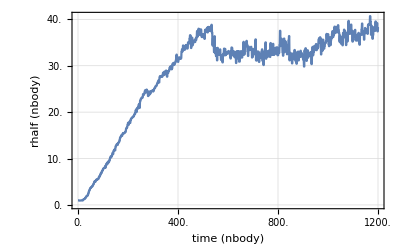

```mathematica
meanRhalfAndTimePlot=ScaledListPlot[meanRhalfAndTime,{$TimeScale,$LengthScale},
FrameLabel->{{"rhalf (nbody)","rhalf (pc)"},{"time (nbody)","time (My)"}},
"ShowAllScales"->True]
```

### Mean rdens

```mathematica
meanRdens=Mean/@DeleteCases[Transpose[data[[All,All,3]]],$Failed,{2}];
```

```mathematica
meanRdensAndTime=Transpose[{timeArray,meanRdens}];
```

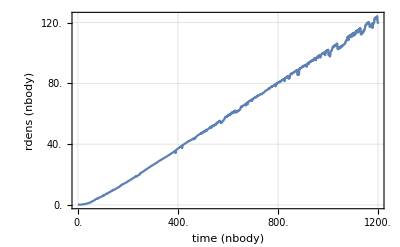

```mathematica
meanRdensAndTimePlot=ScaledListPlot[meanRdensAndTime,{$TimeScale,$LengthScale},
FrameLabel->{{"rdens (nbody)","rdens (pc)"},{"time (nbody)","time (My)"}},"ShowAllScales"->True]
```

## Loading Data

#### Load from OUT3 or MX

```mathematica
(* 8 values: id, pos, vel, mass *)
(* 8 bytes each one *)
```

```mathematica
(numberOfStars*maxNbodyTime*runmax*8*8)/(1024*1024*1024. nbodyStep)
```

0.987053

```mathematica
snapshots=All;
```

```mathematica
(*snapshots=Range[1,maxNbodyTime,10];*)
```

```mathematica
Write[logstream, "computing particles.mx ...."]
```

```mathematica
(* Check also: "particles.bin" *)
If[!FileExistsQ["particles.mx"]
	,
	Print[TimeAndMem[]];
	(*While[Kernels[] == {}, 
		kernels = LaunchKernels[];
		];*)
	kernels = LaunchKernels[];
	Write[logstream, kernels];
	Print["Kernels: ", kernels];
	SetSharedVariable[dirs];
	ParallelEvaluate[AppendTo[$Path, Environment["MYGITDIR"]]];
	ParallelEvaluate[SetDirectory[resultsPath]];
	ParallelNeeds["AstroTools`nbody6`"];
	ParallelNeeds["AstroTools`Utilities`"];
	(particles = 
		Transpose@
		ParallelTable[
			SetDirectory[dirs[[i]]];
			Print["DIR: ", dirs[[i]]];
			{bodys,xs,vs,name} = Flatten[ReadOUT3["OUT3","Snapshots" -> snapshots], 1];
			xs=Partition[#,3]&/@xs;
			vs=Partition[#,3]&/@vs;
			ResetDirectory[]; 
			{bodys,xs,vs,name}
			,
			{i,1,Length[dirs]}]);
	
	Print["Closing kernels ..."];
	CloseKernels[];

	(*-- SAVE to a MX file --*)
	Print["Saving data to MX ... "];
	Print[TimeAndMem[]];
	DumpSave["particles.mx", particles];
	Print[TimeAndMem[]];

	(*-- SAVE to a BIN file --*)
	(* BinarySerializeSave[particles,"particles.bin"]; // AbsoluteTiming *)
	
	,
	
	(*-- Get file from MX --*)
	Print["Loading MX ..."];
	Get["particles.mx"];
] // AbsoluteTiming
```

15:23:32 mem:157.914MB

Kernels: {KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…]}

DIR: ./run-100/

DIR: ./run-11/

DIR: ./run-13/

DIR: ./run-15/

DIR: ./run-17/

DIR: ./run-25/

DIR: ./run-28/

DIR: ./run-36/

DIR: ./run-38/

DIR: ./run-42/

DIR: ./run-45/

DIR: ./run-49/

DIR: ./run-51/

DIR: ./run-53/

DIR: ./run-61/

DIR: ./run-63/

DIR: ./run-68/

DIR: ./run-69/

DIR: ./run-6/

DIR: ./run-70/

DIR: ./run-71/

DIR: ./run-72/

DIR: ./run-73/

DIR: ./run-76/

DIR: ./run-77/

DIR: ./run-83/

DIR: ./run-87/

DIR: ./run-89/

DIR: ./run-93/

DIR: ./run-97/

DIR: ./run-10/

DIR: ./run-12/

DIR: ./run-14/

DIR: ./run-16/

DIR: ./run-20/

DIR: ./run-26/

DIR: ./run-29/

DIR: ./run-37/

DIR: ./run-41/

DIR: ./run-43/

DIR: ./run-47/

DIR: ./run-50/

DIR: ./run-52/

DIR: ./run-55/

DIR: ./run-62/

DIR: ./run-64/

Closing kernels ...

Saving data to MX ...

15:25:10 mem:4.40453GB

15:32:19 mem:3.60917GB

{526.634,Null}

```mathematica
Write[logstream, "particles.mx done!"]
```

```mathematica
(* --- serial computation ---
(particles=
Transpose@
Table[SetDirectory[dirs[[i]]];
Print["DIR: ", dirs[[i]]];
{bodys,xs,vs,name}=Flatten[ReadOUT3["OUT3","Snapshots"->All],1];
xs=Partition[#,3]&/@xs;
vs=Partition[#,3]&/@vs;
ResetDirectory[]; 
{bodys,xs,vs,name}
,{i,1,Length[dirs]}]);//AbsoluteTiming *)
```

#### Mem information

```mathematica
TimeAndMem[]
```

15:32:19 mem:3.60918GB

```mathematica
(*PrintArrayInfo[particles]*)
```

```mathematica
DeleteOuts[500]
```

session mem: 3.60918GB

No Out[] greater than 500MB

```mathematica
$numberOfRunsStatus=Dimensions[particles][[2]]
```

46

## Filtering Invalid Data

### Indexes To Extract Data

```mathematica
nbIndexes=Table[Range[maxNbodyTime/nbodyStep+1],{runmax}];
```

```mathematica
nbIndexes//Dimensions
```

{46,1201}

```mathematica
nbIndexes[[1]]//Short
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,304,305,306,307,308,309,310,311,312,313,314,315,316,317,318,319,320,321,322,323,324,325,326,327,328,329,330,331,332,333,334,335,336,337,338,339,340,341,342,343,344,345,346,347,348,349,350,351,352,353,354,355,356,357,358,359,360,361,362,363,364,365,366,367,368,369,370,371,372,373,374,375,376,377,378,379,380,381,382,383,384,385,386,387,388,389,390,391,392,393,394,395,396,397,398,399,400,401,402,403,404,405,406,407,408,409,410,411,412,413,414,415,416,417,418,419,420,421,422,423,424,425,426,427,428,429,430,431,432,433,434,435,436,437,438,439,440,441,442,443,444,445,446,447,448,449,450,451,452,453,454,455,456,457,458,459,460,461,462,463,464,465,466,467,468,469,470,471,472,473,474,475,476,477,478,479,480,481,482,483,484,485,486,487,488,489,490,491,492,493,494,495,496,497,498,499,500,501,502,503,504,505,506,507,508,509,510,511,512,513,514,515,516,517,518,519,520,521,522,523,524,525,526,527,528,529,530,531,532,533,534,535,536,537,538,539,540,541,542,543,544,545,546,547,548,549,550,551,552,553,554,555,556,557,558,559,560,561,562,563,564,565,566,567,568,569,570,571,572,573,574,575,576,577,578,579,580,581,582,583,584,585,586,587,588,589,590,591,592,593,594,595,596,597,598,599,600,601,602,603,604,605,606,607,608,609,610,611,612,613,614,615,616,617,618,619,620,621,622,623,624,625,626,627,628,629,630,631,632,633,634,635,636,637,638,639,640,641,642,643,644,645,646,647,648,649,650,651,652,653,654,655,656,657,658,659,660,661,662,663,664,665,666,667,668,669,670,671,672,673,674,675,676,677,678,679,680,681,682,683,684,685,686,687,688,689,690,691,692,693,694,695,696,697,698,699,700,701,702,703,704,705,706,707,708,709,710,711,712,713,714,715,716,717,718,719,720,721,722,723,724,725,726,727,728,729,730,731,732,733,734,735,736,737,738,739,740,741,742,743,744,745,746,747,748,749,750,751,752,753,754,755,756,757,758,759,760,761,762,763,764,765,766,767,768,769,770,771,772,773,774,775,776,777,778,779,780,781,782,783,784,785,786,787,788,789,790,791,792,793,794,795,796,797,798,799,800,801,802,803,804,805,806,807,808,809,810,811,812,813,814,815,816,817,818,819,820,821,822,823,824,825,826,827,828,829,830,831,832,833,834,835,836,837,838,839,840,841,842,843,844,845,846,847,848,849,850,851,852,853,854,855,856,857,858,859,860,861,862,863,864,865,866,867,868,869,870,871,872,873,874,875,876,877,878,879,880,881,882,883,884,885,886,887,888,889,890,891,892,893,894,895,896,897,898,899,900,901,902,903,904,905,906,907,908,909,910,911,912,913,914,915,916,917,918,919,920,921,922,923,924,925,926,927,928,929,930,931,932,933,934,935,936,937,938,939,940,941,942,943,944,945,946,947,948,949,950,951,952,953,954,955,956,957,958,959,960,961,962,963,964,965,966,967,968,969,970,971,972,973,974,975,976,977,978,979,980,981,982,983,984,985,986,987,988,989,990,991,992,993,994,995,996,997,998,999,1000,1001,1002,1003,1004,1005,1006,1007,1008,1009,1010,1011,1012,1013,1014,1015,1016,1017,1018,1019,1020,1021,1022,1023,1024,1025,1026,1027,1028,1029,1030,1031,1032,1033,1034,1035,1036,1037,1038,1039,1040,1041,1042,1043,1044,1045,1046,1047,1048,1049,1050,1051,1052,1053,1054,1055,1056,1057,1058,1059,1060,1061,1062,1063,1064,1065,1066,1067,1068,1069,1070,1071,1072,1073,1074,1075,1076,1077,1078,1079,1080,1081,1082,1083,1084,1085,1086,1087,1088,1089,1090,1091,1092,1093,1094,1095,1096,1097,1098,1099,1100,1101,1102,1103,1104,1105,1106,1107,1108,1109,1110,1111,1112,1113,1114,1115,1116,1117,1118,1119,1120,1121,1122,1123,1124,1125,1126,1127,1128,1129,1130,1131,1132,1133,1134,1135,1136,1137,1138,1139,1140,1141,1142,1143,1144,1145,1146,1147,1148,1149,1150,1151,1152,1153,1154,1155,1156,1157,1158,1159,1160,1161,1162,1163,1164,1165,1166,1167,1168,1169,1170,1171,1172,1173,1174,1175,1176,1177,1178,1179,1180,1181,1182,1183,1184,1185,1186,1187,1188,1189,1190,1191,1192,1193,1194,1195,1196,1197,1198,1199,1200,1201}

```mathematica
nbLenIndexes=Length/@nbIndexes
```

{1201,1201,1201,1201,1201,1201,1201,1201,1201,1201,1201,1201,1201,1201,1201,1201,1201,1201,1201,1201,1201,1201,1201,1201,1201,1201,1201,1201,1201,1201,1201,1201,1201,1201,1201,1201,1201,1201,1201,1201,1201,1201,1201,1201,1201,1201}

### Incomplete runs

```mathematica
particles//Dimensions
```

{4,46}

```mathematica
Length/@particles[[4]]//Union
```

{1197,1199,1200,1201}

```mathematica
(* delete runs that have not complete data *)
maxtimes=Length/@particles[[4]]
```

{1201,1201,1201,1200,1197,1201,1201,1201,1199,1200,1201,1200,1201,1201,1201,1200,1199,1200,1201,1200,1201,1201,1201,1200,1201,1201,1200,1201,1201,1200,1201,1201,1200,1200,1201,1199,1201,1200,1201,1199,1200,1200,1201,1200,1201,1201}

```mathematica
delPos1=Position[maxtimes,x_/;x<Max[maxtimes]]
```

{{4},{5},{9},{10},{12},{16},{17},{18},{20},{24},{27},{30},{33},{34},{36},{38},{40},{41},{42},{44}}

```mathematica
delPos1//Length
```

20

#### FIX: Delete complete runs

```mathematica
Extract[dirs,delPos1]
```

{./run-12/,./run-13/,./run-17/,./run-20/,./run-26/,./run-37/,./run-38/,./run-41/,./run-43/,./run-50/,./run-53/,./run-62/,./run-68/,./run-69/,./run-70/,./run-72/,./run-76/,./run-77/,./run-83/,./run-89/}

```mathematica
dirsToDelete=Part[StringSplit[#,$PathnameSeparator]&/@Extract[dirs,delPos1],All,2]
```

{run-12,run-13,run-17,run-20,run-26,run-37,run-38,run-41,run-43,run-50,run-53,run-62,run-68,run-69,run-70,run-72,run-76,run-77,run-83,run-89}

```mathematica
dirsToDelete//Length
```

20

```mathematica
DeleteDirectory[#,DeleteContents->True]&/@dirsToDelete
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

Opt – Update variables to continue computing

```mathematica
particles//Dimensions
```

{4,46}

```mathematica
dirs=Delete[dirs,delPos1];
runmax=Length[dirs];
particles=Delete[#, delPos1]&/@particles;
nbIndexes=Delete[nbIndexes, delPos1];
nbLenIndexes=Length/@nbIndexes;
parameters=Delete[parameters, delPos1];
```

```mathematica
particles//Dimensions
```

{4,26,1201}

```mathematica
nbIndexes//Length
```

26

```mathematica
parameters//Dimensions
```

{26,6}

```mathematica
PrintArrayInfo[particles]
```

Length: 4 MEM: 2.54009GB

### Particles in the same position

#### TEST

```mathematica
particles[[All,All,All,1;;numberOfStars]]//Dimensions
```

{4,26,1201,300}

```mathematica
Clear[ceros];
If[!FileExistsQ["ceros.mx"],
ceros=Reap[
Do[
Print["run: ", run];
Do[
With[
{pe=TotalPotentialEnergy[particles[[1,run,t,All]],particles[[2,run,t,All]]]},
If[pe==0.,Sow[{run,t}];Print["CERO AT: ", run];Break[]]
]
,{t,1,nbLenIndexes[[run]]}
],
{run,1,runmax}]
];
DumpSave["ceros.mx", ceros]
,
(*-- Get file from MX --*)
	Print["Loading MX ..."];
	Get["ceros.mx"];
];//AbsoluteTiming
```

run: 1

run: 2

run: 3

run: 4

run: 5

run: 6

run: 7

run: 8

run: 9

run: 10

run: 11

run: 12

run: 13

run: 14

run: 15

run: 16

run: 17

run: 18

run: 19

run: 20

run: 21

run: 22

run: 23

run: 24

run: 25

run: 26

{199.022,Null}

```mathematica
ceros[[2]]
```

{}

#### Double check

```mathematica
(*invalid=With[{run=7},Reap[Do[
With[
{pe=TotalPotentialEnergy[particles[[1,run,t,All]],particles[[2,run,t,All]]]},
If[pe==0.,Sow[{run,t}]]
]
,{t,1,nbLenIndexes[[run]]}
]]
];*)
```

```mathematica
(*invalid//Short*)
```

```mathematica
(*With[{run=7, time=1100},
Select[GatherBy[Transpose[{particles[[4,run,time,All]],particles[[2,run,time,All]]}],Last],Length[#]>1&]]*)
```

```mathematica
(*With[
{part1=2,
part2=1,
run=46,
interTime=220
},
vel=Table[{#[part1],#[part2]}&@(<|#[[1]]->#[[2]]&/@Transpose[{particles[[4,run,time,All]],particles[[3,run,time,All]]}]|>),{time,1,nbLenIndexes[[run]],1}];
pos=Table[{#[part1],#[part2]}&@(<|#[[1]]->#[[2]]&/@Transpose[{particles[[4,run,time,All]],particles[[2,run,time,All]]}]|>),{time,1,nbLenIndexes[[run]],1}];

{ListLinePlot[{Norm/@vel[[All,1]],Norm/@vel[[All,2]]},
PlotRange->{{0,1000},{0,100}}],
ListLinePlot[{Norm/@pos[[All,1]],Norm/@pos[[All,2]]},
PlotRange->{{0,1000},{0,50000}},Epilog->InfiniteLine[{{interTime,0},{interTime,1}}]]}
]*)
```

```mathematica
(* testing indexes outside particles range *)
```

```mathematica
(*testing1001=Table[#[1001]&@(<|#[[1]]->#[[2]]&/@Transpose[{particles[[4,2,time,All]],particles[[2,2,time,All]]}]|>),{time,1,nbLenIndexes[[2]],1}];*)
```

```mathematica
(*Position[testimg1001,_Missing]*)
```

```mathematica
(*testing1002=Table[#[1002]&@(<|#[[1]]->#[[2]]&/@Transpose[{particles[[4,2,time,All]],particles[[2,2,time,All]]}]|>),{time,1,nbLenIndexes[[2]],1}];*)
```

```mathematica
(*testing1002[[8]]*)
```

#### FIX 1: Delete complete runs

```mathematica
delPos2=If[ceros[[2]]=={},{},Partition[Union[ceros[[2,1]][[All,1]]],1]];
```

```mathematica
delPos2//Short
```

{}

```mathematica
Extract[dirs,delPos2]
```

{}

```mathematica
dirsToDelete=Part[StringSplit[#,$PathnameSeparator]&/@Extract[dirs,delPos2],All,2]
```

{}

```mathematica
dirsToDelete//Length
```

0

```mathematica
DeleteDirectory[#,DeleteContents->True]&/@dirsToDelete;
```

Opt 1 – Delete files to begin from scratch

(* 
	Si dirsToDelete≠0 borrar *.m *.mx 
	generar goodRuns.log y correr nb de nuevo.
*)

FileNames["*.*"]

DeleteFile[#] & /@ FileNames["*.*"]

Opt 2 – Update variables to continue computing

```mathematica
dirs=Delete[dirs,delPos2];
```

```mathematica
runmax=Length[dirs]
```

26

```mathematica
particles//Dimensions
```

{4,26,1201}

```mathematica
particles=Delete[#, delPos2]&/@particles;
```

```mathematica
particles//Dimensions
```

{4,26,1201}

```mathematica
PrintArrayInfo[particles]
```

Length: 4 MEM: 2.54009GB

```mathematica
nbIndexes=Delete[nbIndexes, delPos2];
```

```mathematica
nbIndexes//Length
```

26

```mathematica
nbLenIndexes=Length/@nbIndexes
```

{1201,1201,1201,1201,1201,1201,1201,1201,1201,1201,1201,1201,1201,1201,1201,1201,1201,1201,1201,1201,1201,1201,1201,1201,1201,1201}

```mathematica
parameters//Dimensions
```

{26,6}

```mathematica
parameters=Delete[parameters, delPos2];
```

```mathematica
parameters//Dimensions
```

{26,6}

#### FIX 2: Delete specific snapshots (ruled out)

```mathematica
(* We will delete data only for snapshots containg equal positions *)
```

delPos3 = ceros[[2, 1]]

particles = Delete[#, delPos3] & /@ particles;

timeIndexes[[1, 450]]

Complement[Range[1000], timeIndexes[[1]]]

timeIndexes = Delete[timeIndexes, delPos3];

Complement[Range[1000], timeIndexes[[1]]]

nbLenIndexes = Length /@ timeIndexes

### Particles with index 0 / position 0.

#### TEST

```mathematica
(* Delete time snaphots of incorrect data with ceros in the position vector. *)
(* Very strange issue from nbody *)
```

```mathematica
delPos4=Position[particles[[4]],0][[All,{1,2}]];
```

```mathematica
delPos4//Short
```

{{1,701},{1,702},{3,43},{3,44},{3,45},{3,180},{3,181},{3,1029},{4,309},{4,310},{4,311},{4,312},{4,313},{4,314},{4,315},{4,316},{4,317},{4,318},{4,319},{4,320},{4,321},{4,322},{4,323},{4,324},{4,325},{5,50},{7,502},{7,503},{7,504},{7,505},{7,506},{7,507},{7,508},{9,158},{10,21},{10,31},{10,77},{10,78},{10,79},{10,80},{10,81},{10,82},{10,83},{10,84},{10,85},{10,86},{10,87},{10,88},{10,89},{10,165},{10,166},{10,317},{10,318},{10,319},{10,320},{10,321},{10,1077},{10,1078},{14,18},{14,50},{14,51},{14,221},{14,578},{14,806},{14,807},{14,808},{15,72},{16,47},{17,51},{18,169},{18,808},{18,809},{18,810},{18,811},{18,812},{18,813},{18,814},{18,815},{18,816},{18,817},{18,818},{18,819},{18,820},{18,821},{18,822},{18,823},{18,824},{18,825},{18,826},{18,827},{18,828},{18,829},{18,830},{18,831},{18,832},{18,833},{18,834},{18,835},{18,836},{18,837},{18,838},{18,839},{18,840},{18,841},{18,842},{18,843},{18,844},{18,845},{18,846},{18,847},{18,848},{18,849},{18,850},{18,851},{18,852},{18,853},{18,854},{18,855},{18,856},{18,857},{18,858},{18,859},{18,860},{18,861},{18,862},{18,863},{18,864},{18,865},{18,866},{18,867},{18,868},{18,869},{18,870},{18,871},{18,872},{18,873},{18,874},{18,875},{18,876},{18,877},{18,878},{18,879},{18,880},{18,881},{18,882},{18,883},{18,884},{18,885},{18,886},{18,887},{18,888},{18,889},{18,890},{18,891},{18,892},{18,893},{18,894},{18,895},{18,896},{18,897},{18,898},{18,899},{18,900},{18,901},{18,902},{18,903},{18,904},{18,905},{18,906},{18,907},{18,908},{18,909},{18,910},{18,911},{18,912},{18,913},{18,914},{18,915},{18,916},{18,917},{18,918},{18,919},{18,920},{18,921},{18,922},{18,923},{18,924},{18,925},{20,120},{20,121},{20,122},{20,1170},{20,1171},{20,1172},{20,1173},{20,1174},{20,1175},{20,1176},{20,1177},{21,226},{21,231},{21,232},{21,233},{21,234},{25,227},{25,228}}

```mathematica
delPos4[[All,1]]//Union
```

{1,3,4,5,7,9,10,14,15,16,17,18,20,21,25}

```mathematica
delPos4[[All,1]]//Union//Length
```

15

```mathematica
(* NICE runs *)
Complement[Range[runmax],delPos4[[All,1]]//Union]
```

{2,6,8,11,12,13,19,22,23,24,26}

```mathematica
(* Consistent with non missing IDs *)
moreIDS=Table[Position[Complement[Range[numberOfStars],#]&/@particles[[4,run,All,All]],x_/;x≠{},{1}],{run,runmax}];
Position[moreIDS,{}]//Flatten
```

{2,6,8,11,12,13,19,22,23,24,26}

```mathematica
bad=Partition[delPos4[[All,1]]//Union,1];
good=Partition[Position[moreIDS,{}]//Flatten,1];
```

```mathematica
Write[logstream,"bad runs: ",bad]
```

```mathematica
Write[logstream,"good runs: ",good]
```

```mathematica
badRunsDirs=Part[StringSplit[#,$PathnameSeparator]&/@Extract[dirs,bad],All,2]
```

{run-100,run-11,run-14,run-15,run-25,run-29,run-36,run-49,run-51,run-52,run-55,run-61,run-64,run-6,run-93}

```mathematica
goodRunsDirs=Part[StringSplit[#,$PathnameSeparator]&/@Extract[dirs,good],All,2]
```

{run-10,run-16,run-28,run-42,run-45,run-47,run-63,run-71,run-73,run-87,run-97}

```mathematica
CreateDirectory["./good-runs"];
CreateDirectory["./bad-runs"];
```

```mathematica
CopyDirectory[#,"./good-runs"]&/@goodRunsDirs;
DeleteDirectory[goodRunsDirs,DeleteContents->True];
```

CopyDirectory::filex: Cannot overwrite existing directory «13».

General::stop: Further output of «1» will be suppressed during this calculation.

```mathematica
CopyDirectory[#,"./bad-runs"]&/@badRunsDirs;
DeleteDirectory[badRunsDirs,DeleteContents->True];
```

CopyDirectory::filex: Cannot overwrite existing directory «12».

General::stop: Further output of «1» will be suppressed during this calculation.

## Close

```mathematica
Print["len in goodRubs:: ",Length[StringSplit[Import["goodRuns.log","String"],"\n"]]];
Print["len in particles:: ",$numberOfRunsStatus]
If[$numberOfRunsStatus>50,
Import["!../run2end.sh","String"];
Print["deleted: ",FileNames[{"*.m","*.mx"}]];
DeleteFile[#]&/@FileNames[{"*.m","*.mx"}]
]
```

len in goodRubs:: 46

len in particles:: 46

```mathematica
Write[logstream, "End succesfully ...."]
```

```mathematica
Close[logstream]
```

/home/cesarg/git/workspace/nbody6/isolated/scripts/FilterAndTest/nbstatus300.log